# 共引用と書誌結合

## Nav: top

## 共引用 (co-citation)

同じ記事に引用されている記事間の関係。ひとつの論文(A)が、3つの他の論文(C,D,E)を引用しているとき、C、D、Eが共引用の関係にある(図 1)。

## 書誌結合 (bibliographic coupling)

同じ記事を引用している記事間の関係。複数の記事(A,B)がひとつの共通の論文(C)を引用しているとき、A、Bの関係が書誌結合の関係にある(図 1)。

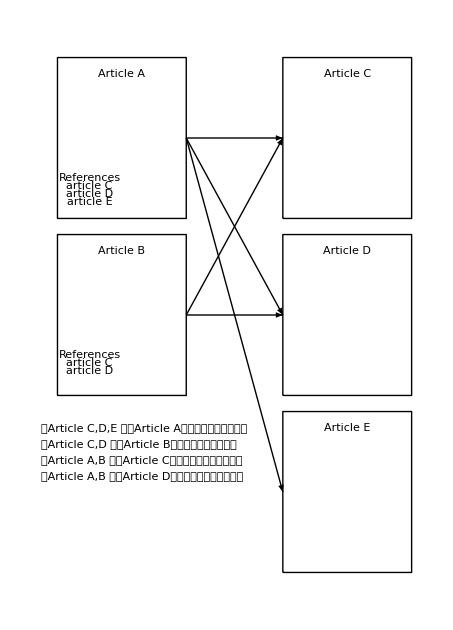

図 1

以上webコンテンツ

## 図表作成

```mathematica
obj["size"]={{0,0},{0,10},{8,10},{8,0},{0,0}}
```

{{0,0},{0,10},{8,10},{8,0},{0,0}}

```mathematica
obj["art-A"]={Line[Map[#+{1,1}&,obj["size"]]],Text["Article A",{5,10}],Text["References",{3,3.5}],Text["article C",{3,3.}],Text["article D",{3,2.5}],Text["article E",{3,2.}]}
```

{Line[{{1,1},{1,11},{9,11},{9,1},{1,1}}],Text[Article A,{5,10}],Text[References,{3,3.5}],Text[article C,{3,3.}],Text[article D,{3,2.5}],Text[article E,{3,2.}]}

```mathematica
obj["art-B"]={Line[Map[#+{1,-10}&,obj["size"]]],Text["Article B",{5,10}-{0,11}],Text["References",{3,3.5}-{0,11}],Text["article C",{3,3.}-{0,11}],Text["article D",{3,2.5}-{0,11}]}
```

{Line[{{1,-10},{1,0},{9,0},{9,-10},{1,-10}}],Text[Article B,{5,-1}],Text[References,{3,-7.5}],Text[article C,{3,-8.}],Text[article D,{3,-8.5}]}

```mathematica
obj["art-C"]={Line[Map[#+{15,1}&,obj["size"]]],Text["Article C",{5,10}-{-14,0}]}
```

{Line[{{15,1},{15,11},{23,11},{23,1},{15,1}}],Text[Article C,{19,10}]}

```mathematica
obj["art-D"]={Line[Map[#+{15,-10}&,obj["size"]]],Text["Article D",{5,10}-{-14,11}]}
```

{Line[{{15,-10},{15,0},{23,0},{23,-10},{15,-10}}],Text[Article D,{19,-1}]}

```mathematica
obj["art-E"]={Line[Map[#+{15,-21}&,obj["size"]]],Text["Article E",{5,10}-{-14,22}]}
```

{Line[{{15,-21},{15,-11},{23,-11},{23,-21},{15,-21}}],Text[Article E,{19,-12}]}

```mathematica
arrow["A-C"]=Arrow[{{9,6},{15,6}}]
```

Arrow[{{9,6},{15,6}}]

```mathematica
arrow["A-D"]=Arrow[{{9,6},{15,-5}}]
```

Arrow[{{9,6},{15,-5}}]

```mathematica
arrow["A-E"]=Arrow[{{9,6},{15,-16}}]
```

Arrow[{{9,6},{15,-16}}]

```mathematica
arrow["B-C"]=Arrow[{{9,-5},{15,6}}]
```

Arrow[{{9,-5},{15,6}}]

```mathematica
arrow["B-D"]=Arrow[{{9,-5},{15,-5}}]
```

Arrow[{{9,-5},{15,-5}}]

```mathematica
regend[1]=Text["・Article C,D,E が、Article Aを通じて共引用の関係",{0,-12},{-1,0}]
```

Text[・Article C,D,E が、Article Aを通じて共引用の関係,{0,-12},{-1,0}]

```mathematica
regend[2]=Text["・Article C,D が、Article Bを通じて共引用の関係",{0,-13},{-1,0}]
```

Text[・Article C,D が、Article Bを通じて共引用の関係,{0,-13},{-1,0}]

```mathematica
regend[3]=Text["・Article A,B が、Article Cを通じて書誌結合の関係",{0,-14},{-1,0}]
```

Text[・Article A,B が、Article Cを通じて書誌結合の関係,{0,-14},{-1,0}]

```mathematica
regend[4]=Text["・Article A,B が、Article Dを通じて書誌結合の関係",{0,-15},{-1,0}]
```

Text[・Article A,B が、Article Dを通じて書誌結合の関係,{0,-15},{-1,0}]

```mathematica
Graphics[{obj["art-A"],obj["art-B"],obj["art-C"],obj["art-D"],obj["art-E"],arrow["A-C"],arrow["A-D"],arrow["A-E"],arrow["B-C"],arrow["B-D"],regend[1],regend[2],regend[3],regend[4]}]
```

-Graphics-